```mathematica
param={l1->5.59,l2->5.59,m1->300,m2->300,mb->419725,mO->3000,r->0.12,γ->0.5};
```

```mathematica
p={xb[t],yb[t],θ0[t],q1[t],q2[t]};
```

```mathematica
M'={{420325+2915.431042203624 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2,-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])],1/2 (-5031. Sin[q1[t]+θ0[t]]-1677. Sin[q1[t]+q2[t]+θ0[t]])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (2915.431042203624 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2),1/2 (-5031. Sin[q1[t]+θ0[t]]-1677. Sin[q1[t]+q2[t]+θ0[t]])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (2915.431042203624 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2),-838.5 Sin[q1[t]+q2[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]] (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (2915.431042203624 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2)},{-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])],420325+0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+2915.431042203624 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2,1/2 (5031. Cos[q1[t]+θ0[t]]+1677. Cos[q1[t]+q2[t]+θ0[t]])+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+2915.431042203624 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2),1/2 (5031. Cos[q1[t]+θ0[t]]+1677. Cos[q1[t]+q2[t]+θ0[t]])+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+2915.431042203624 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2),838.5 Cos[q1[t]+q2[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+5.59 Cos[q1[t]+q2[t]+θ0[t]] (0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+2915.431042203624 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2)},{1/2 (-5031. Sin[q1[t]+θ0[t]]-1677. Sin[q1[t]+q2[t]+θ0[t]])-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]),1/2 (5031. Cos[q1[t]+θ0[t]]+1677. Cos[q1[t]+q2[t]+θ0[t]])+2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]),1/6 (111876.41999999998+56246.58 Cos[q2[t]])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])),1/3 (46872.149999999994+28123.29 Cos[q2[t]])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])),279.5 (11.18+16.77 Cos[q2[t]])+5.59 Cos[q1[t]+q2[t]+θ0[t]] (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))},{1/2 (-5031. Sin[q1[t]+θ0[t]]-1677. Sin[q1[t]+q2[t]+θ0[t]])-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]),1/2 (5031. Cos[q1[t]+θ0[t]]+1677. Cos[q1[t]+q2[t]+θ0[t]])+2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]),1/3 (46872.149999999994+28123.29 Cos[q2[t]])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])),1/3 (46872.149999999994+28123.29 Cos[q2[t]])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])),279.5 (11.18+16.77 Cos[q2[t]])+5.59 Cos[q1[t]+q2[t]+θ0[t]] (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))},{-838.5 Sin[q1[t]+q2[t]+θ0[t]]-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]),838.5 Cos[q1[t]+q2[t]+θ0[t]]+2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]),279.5 (11.18+16.77 Cos[q2[t]])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])),279.5 (11.18+16.77 Cos[q2[t]])+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])),3124.8099999999995+5.59 Cos[q1[t]+q2[t]+θ0[t]] (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]))}};
```

```mathematica
C'={xb'[t] (0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])-83.96441401546437 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+yb'[t] (41.982207007732185 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2 (q1'[t]+q2'[t]+θ0'[t])+0.6045437809113435 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+q2'[t] (-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (2915.431042203624 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2) (q1'[t]+q2'[t]+θ0'[t]))+1/2 (-5031. Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-1677. Cos[q2[t]] Cos[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2+1677. Sin[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)+q1'[t] ((2915.431042203624 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((2915.431042203624 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+q2'[t] (-5.59 Sin[q1[t]+q2[t]+θ0[t]] (0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])-83.96441401546437 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+5.59 Cos[q1[t]+q2[t]+θ0[t]] (41.982207007732185 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2 (q1'[t]+q2'[t]+θ0'[t])+0.6045437809113435 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t])))+q1'[t] ((-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])-83.96441401546437 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (41.982207007732185 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2 (q1'[t]+q2'[t]+θ0'[t])+0.6045437809113435 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])-83.96441401546437 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (41.982207007732185 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2 (q1'[t]+q2'[t]+θ0'[t])+0.6045437809113435 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))),yb'[t] (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])+83.96441401546437 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+xb'[t] (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2 (q1'[t]+q2'[t]+θ0'[t])+41.982207007732185 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (q1'[t]+q2'[t]+θ0'[t])-0.6045437809113435 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+q2'[t] (-5.59 Cos[q1[t]+q2[t]+θ0[t]] (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+2915.431042203624 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2) (q1'[t]+q2'[t]+θ0'[t]))+1/2 (-5031. Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-1677. Cos[q1[t]+θ0[t]] Sin[q2[t]] (q1'[t]+q2'[t]+θ0'[t])^2-1677. Cos[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)+q1'[t] ((-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+2915.431042203624 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]+20.991103503866093 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]+20.991103503866093 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2+2915.431042203624 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)^2+0.15113594522783588 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]^2) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+q1'[t] ((5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])+83.96441401546437 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2 (q1'[t]+q2'[t]+θ0'[t])+41.982207007732185 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (q1'[t]+q2'[t]+θ0'[t])-0.6045437809113435 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])+83.96441401546437 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))+(-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2 (q1'[t]+q2'[t]+θ0'[t])+41.982207007732185 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (q1'[t]+q2'[t]+θ0'[t])-0.6045437809113435 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t])))+q2'[t] (5.59 Cos[q1[t]+q2[t]+θ0[t]] (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])+83.96441401546437 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (q1'[t]+q2'[t]+θ0'[t])+0.30227189045567177 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-0.30227189045567177 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2 (q1'[t]+q2'[t]+θ0'[t])+41.982207007732185 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (q1'[t]+q2'[t]+θ0'[t])-0.6045437809113435 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (q1'[t]+q2'[t]+θ0'[t]))),-4687.215 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])+xb'[t] (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+yb'[t] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+q2'[t] (-5.59 Sin[q1[t]+q2[t]+θ0[t]] (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (q1'[t]+q2'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (q1'[t]+q2'[t]+θ0'[t]))+q1'[t] ((-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+q2'[t] (-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+5.59 Cos[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])))+q1'[t] ((-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))),-4687.215 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])+xb'[t] (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+yb'[t] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+q2'[t] (-5.59 Sin[q1[t]+q2[t]+θ0[t]] (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (q1'[t]+q2'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (q1'[t]+q2'[t]+θ0'[t]))+q1'[t] ((-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+q2'[t] (-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+5.59 Cos[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])))+q1'[t] ((-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.11829652996845424 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]-0.11829652996845424 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (0.9858044164037855 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]])+0.007097791798107255 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.9858044164037855 (5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)+0.007097791798107255 (-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))),4687.215 Sin[q2[t]] (q1'[t]+θ0'[t])^2+xb'[t] (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+yb'[t] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+q2'[t] (-5.59 Sin[q1[t]+q2[t]+θ0[t]] (2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (q1'[t]+q2'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (q1'[t]+q2'[t]+θ0'[t]))+q1'[t] ((-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+2957.4132492113563 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]))+(2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]])+21.293375394321764 Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])+2957.4132492113563 (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])])) (-5.59 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-5.59 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])))+q2'[t] (-5.59 Sin[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+5.59 Cos[q1[t]+q2[t]+θ0[t]] (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])))+q1'[t] ((-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])))+θ0'[t] ((-5.59 Sin[q1[t]+θ0[t]]-5.59 Sin[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])-85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t]))+(5.59 Cos[q1[t]+θ0[t]]+5.59 Cos[q1[t]+q2[t]+θ0[t]]) (-2.5552050473186116 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (0.6612776025236592 Cos[q1[t]+q2[t]+θ0[t]] Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]+0.6612776025236592 Sin[q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]) (q1'[t]+q2'[t]+θ0'[t])+42.58675078864353 Cos[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])] (-5.510646687697161 (1+0.0144 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2) Sin[q1[t]+q2[t]+θ0[t]]+0.039676656151419555 Cos[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])+85.17350157728706 Cos[3.141592653589793+q1[t]+q2[t]+θ0[t]] Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]] (5.510646687697161 Cos[q1[t]+q2[t]+θ0[t]] (1+0.0144 Sin[3.141592653589793+q1[t]+q2[t]+θ0[t]]^2)-0.039676656151419555 Sin[q1[t]+q2[t]+θ0[t]] Sin[2 (3.141592653589793+q1[t]+q2[t]+θ0[t])]) (q1'[t]+q2'[t]+θ0'[t])))};
```

```mathematica
eqMotion=M'.D[p,t,t]+C';
```

```mathematica
Mtt=M'[[1;;3,1;;3]];
Mtr=M'[[1;;3,4;;5]];
Mrt=M'[[4;;5,1;;3]];
Mrr=M'[[4;;5,4;;5]];
Ct=C'[[1;;3]];
Cr=C'[[4;;5]];
```

```mathematica
Mtilde=Mrr-Mrt.Inverse[Mtt].Mtr;
Ctilde=Cr-Mrt.Inverse[Mtt].Ct;
```

```mathematica
Kp=1IdentityMatrix[2];
Kv=2 Sqrt[Kp];
```

```mathematica
q10=0;
q20=π/2;
```

```mathematica
pd={q10,q20};
pd'={0,0};
```

```mathematica
U=-(Mtilde).(Kv.(D[p[[4;;5]],t]-pd')+Kp.(p[[4;;5]]-pd))+Ctilde;
```

```mathematica
eqMotionControl1=M'[[1,1;;5]].D[p,t,t]+C'[[1]];
eqMotionControl2=M'[[2,1;;5]].D[p,t,t]+C'[[2]];
eqMotionControl3=M'[[3,1;;5]].D[p,t,t]+C'[[3]];
eqMotionControl4=M'[[4,1;;5]].D[p,t,t]+C'[[4]]-U[[1]];
eqMotionControl5=M'[[5,1;;5]].D[p,t,t]+C'[[5]]-U[[2]];
```

```mathematica
NDinitialCondition={xb[0]==3,yb[0]==4,θ0[0]==π/2,q1[0]==q10,q2[0]==q20,xb'[0]==1,yb'[0]==1,θ0'[0]==1,q1'[0]==1,q2'[0]==1};
```

```mathematica
solMotionControl=NDSolve[{(eqMotionControl1/.param)==0,(eqMotionControl2/.param)==0,(eqMotionControl3/.param)==0,(eqMotionControl4/.param)==0,(eqMotionControl5/.param)==0,NDinitialCondition},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

Metto a confronto la soluzione trovata risolvendo numericamente le cinque equazioni differenziali con quella ottenuta scrivendo direttamente la soluzione qui sotto:

```mathematica
sol1=DSolve[{D[q1[t],t,t]+Kv[[1,1]] D[q1[t],t]+Kp[[1,1]](q1[t]-q10)==0,q1[0]==q10,q1'[0]==1},q1[t],t]
sol2=DSolve[{D[q2[t],t,t]+Kv[[2,2]] D[q2[t],t]+Kp[[2,2]](q2[t]-q20)==0,q2[0]==q20,q2'[0]==1},q2[t],t]
```

{{q1[t]→ⅇ^-t t}}

{{q2[t]→1/2 ⅇ^-t (ⅇ^t π+2 t)}}

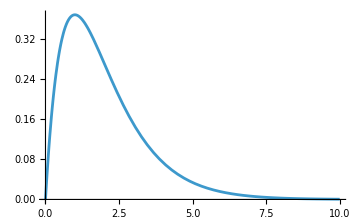
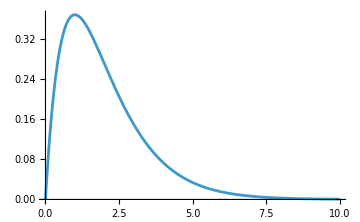

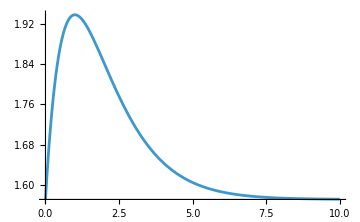
-Graphics--Graphics-

```mathematica
Row[{Plot[{q1[t]/.sol1},{t,0,10},ImageSize->Medium],Plot[{q1[t]/.solMotionControl},{t,0,10},ImageSize->Medium]}]
Row[{Plot[{q2[t]/.sol2},{t,0,10},ImageSize->Medium],Plot[{q2[t]/.solMotionControl},{t,0,10},ImageSize->Medium]}]
```

Sono uguali.